Partiendo de la definición para el momento de freeze-out x_f=ln[(2+c)λ α c]-(n+1/2)ln{ln[(2+c)λ α c]} según E. Kolb y M. Turner en “The Early Universe”, encontramos una rela.08ción entre x_f y λ. Considerando n=0 y escogiendo c(c+2)=n+1, logramos simplificar nuestra expresión a x_f=ln[λ α]-1/2 ln{ln(λ α)}, donde α=0.145 g/(g_(*s)).

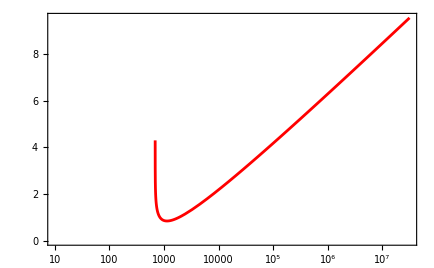

```mathematica
Clear["Global`*"]
xf[λ_]:=Log[λ a ]-1/2 Log[Log[λ a ]];
a=0.145(g/gs);
g=1;
gs=100;
Yinf[λ_]:=xf[λ]/λ;
LogLinearPlot[{xf[λ]},{λ,10,10^7.5},FrameStyle->Black,PlotStyle->{Red},Frame->True,FrameLabel->{"",""},LabelStyle->Medium,GridLines->Automatic]
```